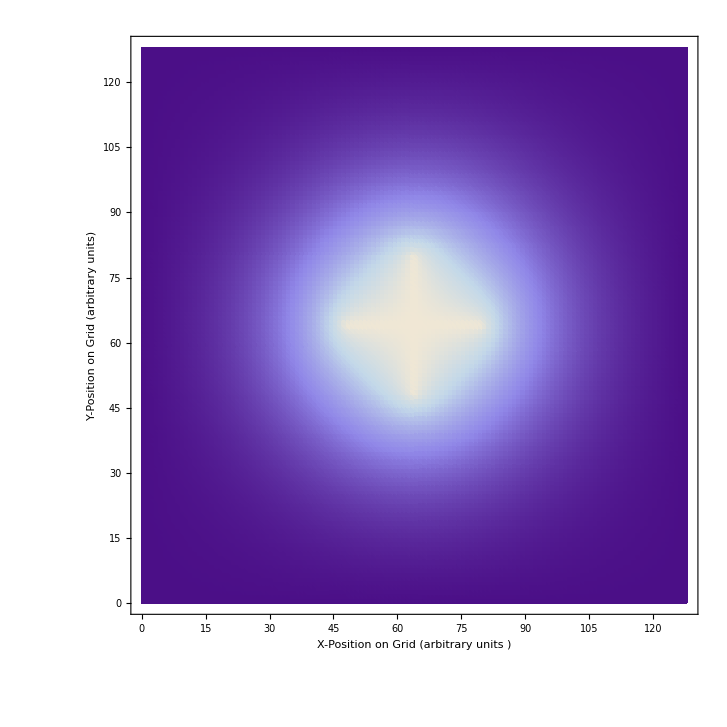

```mathematica
dataG = Import["/home/dk0r/csv/g/gaussSeidel700.csv"];
densityG = ListDensityPlot[dataG,LabelStyle->{FontSize->16},Frame->True,FrameLabel->{"X-Position on Grid (arbitrary units )","Y-Position on Grid (arbitrary units)"}]
```

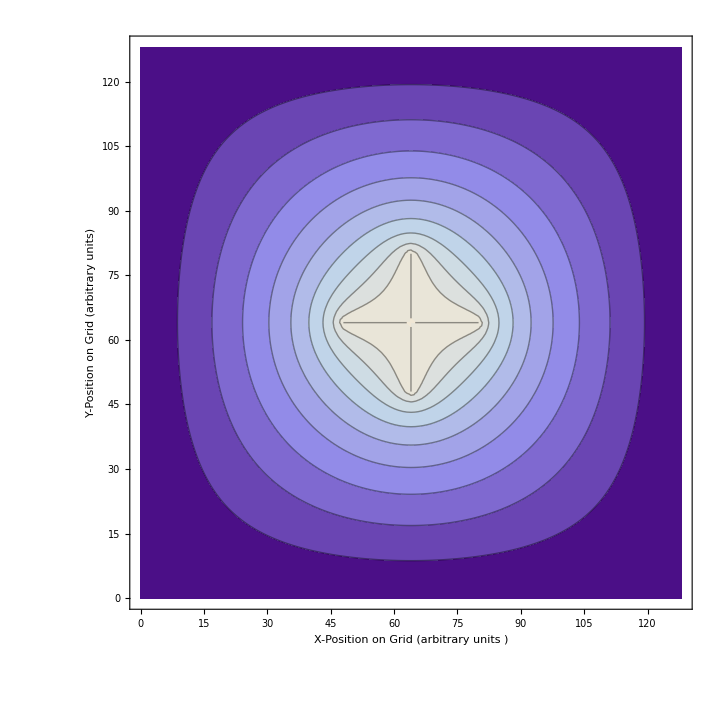

```mathematica
data = Import["/home/dk0r/csv/sor/sor7000.csv"];
contour = ListContourPlot[data,LabelStyle->{FontSize->16},Frame->True,FrameLabel->{"X-Position on Grid (arbitrary units )","Y-Position on Grid (arbitrary units)"}]
```

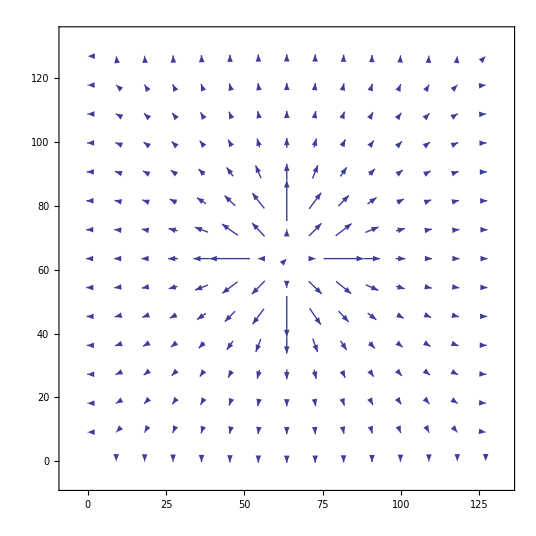

```mathematica
vec=Import["/home/dk0r/csv/e/efield1711.csv"];
vector = ListVectorPlot[vec]
```

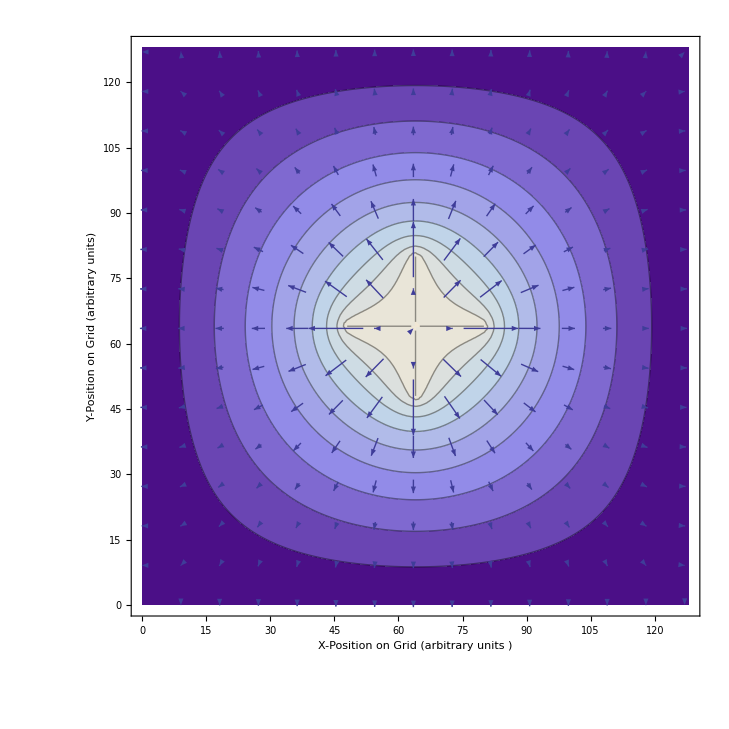

```mathematica
Show[contour, vector]
```

```mathematica
test = Import["/home/dk0r/csv/sor/sor1506.csv"];
vec=Import["/home/dk0r/csv/e/efield1507.csv"];
```

```mathematica
density1 = ListDensityPlot[test];
contour1 = ListContourPlot[test];
vector1 = ListVectorPlot[vec];
```

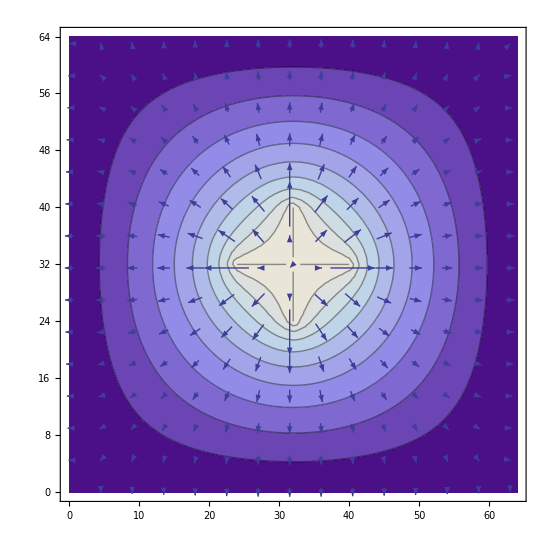

```mathematica
Show[density1,contour1,vector1]
```

```mathematica
omega = Import["/home/dk0r/csv/save/omega.csv"];
```

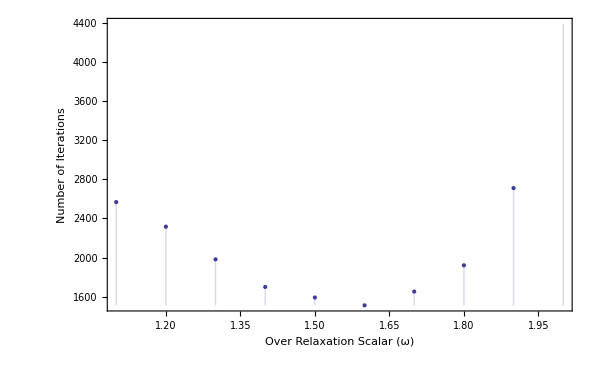

```mathematica
ListPlot[omega,LabelStyle->{FontSize->15},Frame->True,Filling -> Axis,FrameLabel->{"Over Relaxation Scalar (ω)","Number of Iterations"}]
```

```mathematica
test2 = Import["/home/dk0r/csv/sor/sor102.csv"];
vec2=Import["/home/dk0r/csv/e/efield103.csv"];
```

```mathematica
density2 = ListDensityPlot[test];
contour2 = ListContourPlot[test];
vector2 = ListVectorPlot[vec];
```

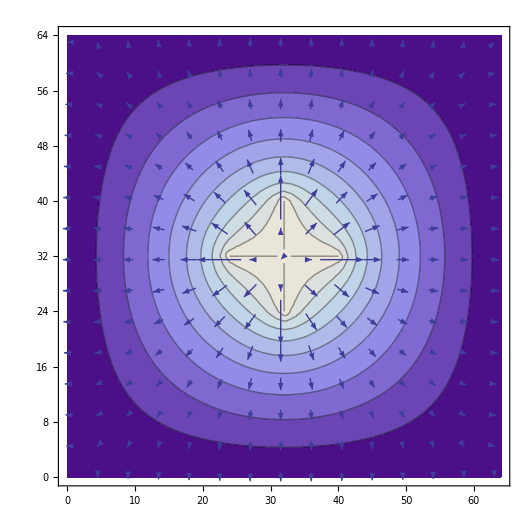

```mathematica
Show[density2,contour2,vector2]
```

```mathematica
temp = Import["/home/dk0r/csv/temp/temp500.csv"];
plot = ListDensityPlot[temp]
ListContourPlot[temp]
```

```mathematica
pot = Import["/home/dk0r/git/comp-phys/HW_5/potentialDrop.csv"];
```

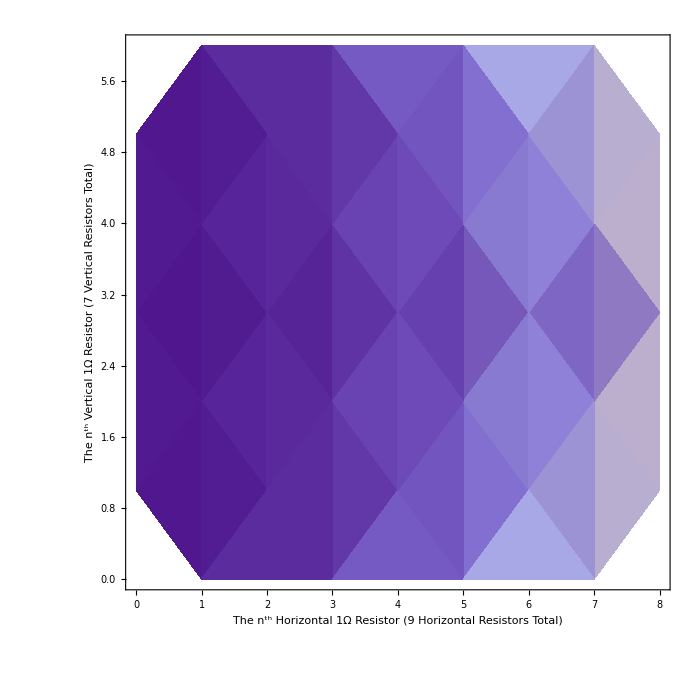

```mathematica
ListDensityPlot[pot,LabelStyle->{FontSize->16},Frame->True,FrameLabel->{"The n^th Horizontal 1Ω Resistor (9 Horizontal Resistors Total)","The n^th Vertical 1Ω Resistor (7 Vertical Resistors Total)"}]
```

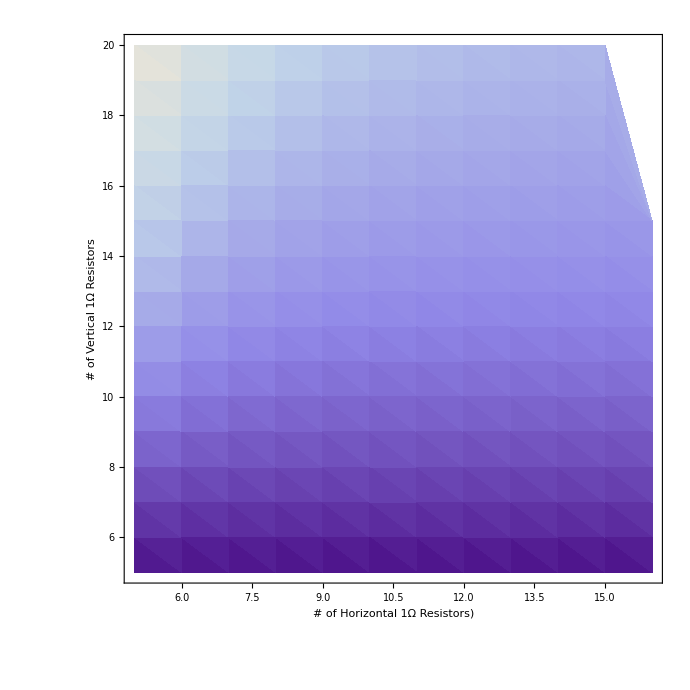

```mathematica
equiv = Import["/home/dk0r/git/comp-phys/HW_5/equivResVSxy.csv"];
ListDensityPlot[equiv, LabelStyle->{FontSize->16},Frame->True,FrameLabel->{"# of Horizontal 1Ω Resistors)","# of Vertical 1Ω Resistors"}]
```

```mathematica
timeGJ = Import["/home/dk0r/git/comp-phys/HW_5/timeGaussJordan.csv"];
```

```mathematica
GJ=ListPlot3D[time]
```

-Graphics3D-

```mathematica
timeLU = Import["/home/dk0r/git/comp-phys/HW_5/timeLUdecomp.csv"];
LU = ListPlot3D[timeLU, PlotStyle -> Green]
```

-Graphics3D-

```mathematica
Show[GJ, LU, LabelStyle->{FontSize->16},Axes->True,AxesLabel->{"# of Horizontal 1Ω Resistors","# of Vertical 1Ω Resistors","Time (µS)"}]
```

-Graphics3D-